# Titlepage Fancy Plot

Fuer die Titelseite der Masterarbeit soll eine kleine Abbildung zu sehen sein, die etwa umreisst, was in der Arbeit drin ist.
Ich dachte an einen DeSitter-Kern in einem Schwarzschild-BH.

Konkret soll es sich um ein embedding Diagram handeln. Dieses Notebook beinhaltet aber (noch) kein embedding Diagram. Das wird, weil es hier so falsch ist, an anderer Stelle behandelt.

```mathematica
SetDirectory[NotebookDirectory[]];
cm=72/2.54;
```

## Modell (achtung, nur g_00, nicht Embedding Diagram)

Dies ist “noch” bloß g00. Dies ist kein richtiges embedding Diagram.

r^3 (1/2+r^α)^(-3/α)

r^2 (1/2+r^((3 Log[3])/(2 Log[2])))^(-(2 Log[2])/Log[3])

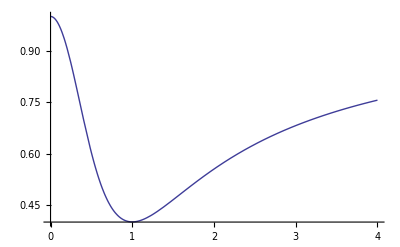

```mathematica
hα[r_,α_] = r^3 / (r^α + 1/2)^(3/α)
α0 = 3/Log[2] Log[3]/2;
V[r_] = hα[r,α0] / r
g00[r_] = 1- V[r];
g00SM[r_] = 1 - 1/r ; 
Plot[g00[r],{r,0,4}]
```

1-(Piecewise[{{2 r^2, r≤1}, {2/r, True}}])

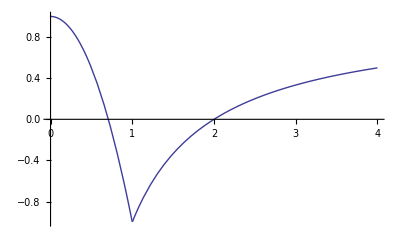

```mathematica
desitterG00[r_] =1- Piecewise[{{2 r^2, r≤ 1}, {2/r, True}}]
Plot[desitterG00[r],{r,0,4}]
```

1-(Piecewise[{{3-r^2, r≤1}, {2/r, True}}])

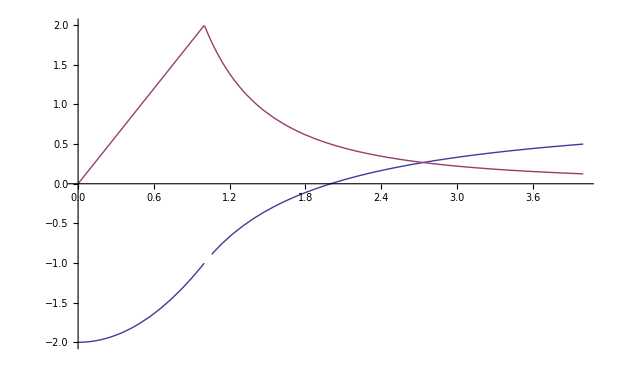

```mathematica
perfectG00[r_] =1- Piecewise[{{-r^2+3, r≤ 1}, {2/r, True}}]
Plot[{perfectG00[r], perfectG00'[r]},{r,0,4}]
```

```mathematica
realG00[r_] = 1- 2/r
```

1-2/r

## 3D-Plots, technisch.

Das liest sich super und funktioniert prima, ist nur auch kein embedding Diagram:

```mathematica
(* maximales r bzw eher maximales x, y *)
rM=2.5;
(* Einsichtswinkel und abgerundete Ecken *)
clipRange = Not[x≥ 0 ∧ y≤0]∧ Norm[{x,y},5] ≤ rM
(* Boundary Style *)
boundstyle= {Thick, GrayLevel[0.4]};
```

!(x≥0&&y≤0)&&(Abs[x]^5+Abs[y]^5)^(1/5)≤2.5

```mathematica
p1=Plot3D[With[{r=Norm[{x,y}]},
1-2 r^2 (* <- hat saubere Kanten als: desitterG00[r]*)
],{x,-rM,rM},{y,-rM,rM},Mesh->Automatic,MeshStyle->LightGray,
PlotStyle-> {Opacity[0.5], {Red,Opacity[0.1]}},
ImageSize-> Large,
RegionFunction-> Function[{x,y,z},clipRange ∧ Norm[{x,y}]≤ 1],
PlotRange-> {-2,1},
Boxed-> False, Axes->False,
ColorFunction-> "BlueGreenYellow",
BoundaryStyle->boundstyle
(*MeshFunctions -> {Norm[{#1,#2}]&, #2&}*)(*klappt nicht richtig*)
]
```

-Graphics3D-

```mathematica
p2=Plot3D[With[{r=Norm[{x,y}]},{
realG00[r]
}
],{x,-rM,rM},{y,-rM,rM},Mesh->Automatic,MeshStyle->LightGray,
PlotStyle-> {Opacity[0.5], {Red,Opacity[0.1]}},
ImageSize-> Large,
RegionFunction-> Function[{x,y,z}, clipRange],
PlotRange-> {-2,1},
Boxed-> False, Axes->False,PlotRangePadding->0,
ColorFunction-> "LakeColors",
ViewAngle-> .41,
BoundaryStyle->boundstyle,
ClippingStyle-> None
(*MeshFunctions -> {Norm[{#1,#2}]&, #2&}*)(*klappt nicht richtig*)
]
```

-Graphics3D-

```mathematica
myDisk[{x_,y_,z_},r_]:=Polygon@Table[{x,y,z}+r {Cos[ϕ],Sin[ϕ],0}//N,{ϕ,0,2 π,2 π/200}]
disk =Graphics3D[{Opacity[0.3],Red, EdgeForm@{Thick,Red,Opacity[0.5]},myDisk[{0,0,-1},1]}];
fig=Show[p1,p2,disk]
(* Extract/Read out the current viewing parameters e.g. by //Options *)
```

-Graphics3D-

```mathematica
-Graphics3D-//Options
```

{BoxRatios→{1,1,0.4},Boxed→False,ImageSize→{576.,398.008},Lighting→Neutral,Method→{ShrinkWrap→True},PlotRange→{{-2.5,2.5},{-2.5,2.5},{-2,1}},PlotRangePadding→{Scaled[0.02],Scaled[0.02],Automatic},ViewPoint→{1.67291,-2.81445,0.854546},ViewVertical→{0.194656,-0.312627,2.32429}}

```mathematica
fig=Show[fig, ViewPoint->{1.67291377055367,-2.814446783461977,0.8545459726383529},ViewVertical->{0.194655584674921,-0.3126270326950553,2.324292287158541}]
```

-Graphics3D-

```mathematica
figPX=ImageCrop@Rasterize[fig, ImageSize-> 40cm]
Export["../figures/titlepage-3d.png", Show@figPX]
```

-Graphics-

../figures/titlepage-3d.png

## Plot zur Erläuterung auf der zweiten Seite

Auch das ist ein hübscher Plot, aber kein embedding Diagram

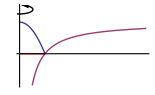

```mathematica
(* Circle replacement with arrows *)
circle[o_,r_,{a_,b_}, res_:100]:=Arrow@Table[{Cos[k],Sin[k]}*r+o,{k,a,b,(b-a)/res}];
fig=Plot[Evaluate[{
If[r≤ 1,1-2 r^2 ,],
realG00[r]
}+1],{r,0,5}, PlotRange-> {-2,3},
Ticks->None,
AxesStyle->Directive@{Opacity[0.5],Gray,Arrowheads[{0.0,0.03}]},
ImageSize-> 5.5cm,
Epilog-> {
Red,
Line@{{0,0},{1,0}},
Black,
Arrowheads[{0.0,0.03}],
circle[{0,2.8}, 0.35 {1.5,0.8}, {0,1.7}π+3/4π]
},
PlotRangeClipping->False,
PlotRangePadding->0.6
]
```

```mathematica
Export["../figures/titlepage-explain.pdf", fig]
```

../figures/titlepage-explain.pdf